# Electrode Voltage Calculation

- Imports electrode geometry from a .json file with the coordinates of named polygons representing the electrodes. The polygons must be oriented counterclockwise, and one of them should have name “RF” (the rf electrode(s))
- calculates DC potentials up to the 2nd derivative, pseudopotential up to the 2nd derivative, 3rd and 4th derivative of DC potentials along the trap axis (x), potential of the cover plane (mesh grid) up to the 2nd derivative
- exports all computed potentials in (very big) python functions

### Example json file

{
“E1”: [
    [-435.0, 102.5],
    [-315.0, 102.5],
    [-315.0, 1102.5],
    [-420.0, 1595.0],
    [-420.0, 1745.0],
    [-570.0, 1745.0],
    [-570.0, 1595.0],
    [-435.0, 1102.5],
    [-435.0, 102.5]
  ],
  ....,
  “RF”: [
    [-310.0, 102.5],
    [-190.0, 102.5],
    [-190.0, 1102.5],
    [-255.0, 1595.0],
    [-255.0, 1745.0],
    [-405.0, 1745.0],
    [-405.0, 1595.0],
    [-310.0, 1102.5],
    [-310.0, 102.5]
  ],
  }

## Initialization

### Directory Options

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Scratch\pytrans-examples\models\surface_trap\data\SurfacePattern

### Load Packages

```mathematica
<<SurfacePattern`
```

Attributes::locked: Symbol SurfacePatternVersion is locked.

Attributes::locked: Symbol CoverPlane is locked.

Attributes::locked: Symbol FourierPattern is locked.

General::stop: Further output of Attributes::locked will be suppressed during this calculation.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::nocomp: A C compiler cannot be found on your system. Please consult the documentation to learn how to set up suitable compilers.

General::stop: Further output of CCompilerDriver`CreateLibrary::nocomp will be suppressed during this calculation.

Compile::nogen: A library could not be generated from the compiled function.

General::stop: Further output of Compile::nogen will be suppressed during this calculation.

```mathematica
SurfacePatternVersion
```

2.4

### Error Handling

```mathematica
Off[ClebschGordan::tri,ClebschGordan::phy]
```

### Physical Constants and Units

```mathematica
AMU=1.6605402 10^-27;
ee=1.60217733*10^-19;

m=1.;μm=10^-6 m;mm=10^-3 m;cm=10^-2 m;nm=10^-9 m;km=10^3 m;
```

### Ion specifics

```mathematica
M9Be=9.012 AMU;
M40Ca = 39.963 AMU;
M43Ca = 42.959 AMU;
```

## Experimental Quantities

### Definitions of geometric lengths and ratios

### Electrode layout

#### Trap electrodes

```mathematica
data = Import["D:\\Scratch\\pytrans-examples\\models\\surface_trap\\surface_trap_geometry.json"];
data = Table[Keys[r] -> Values[r] μm, {r, data}]; (*convert from μm*)
Labels = Keys[data]
LabelsDC = Delete[Labels, Position[Labels, "RF"]];
CoordsDC = LabelsDC/.data;
CoordsRF = {"RF"}/.data;
PosLabelsDC[s_]:=Position[LabelsDC,s]⟦1,1⟧;
```

{DCintop,DCinbot,RF,DCtop1,DCtop2,DCtop3,DCtop4,DCtop5,DCbot1,DCbot2,DCbot3,DCbot4,DCbot5}

Plot the shape of each electrode.

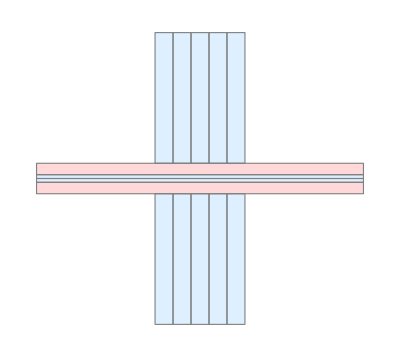

```mathematica
Graphics[{EdgeForm[Gray],LightBlue, Table[Polygon[c], {c, CoordsDC}], LightRed, Table[Polygon[c], {c, CoordsRF}]}]
```

#### Cover plane electrode

```mathematica
H=6mm; (* Height of cover plane. *)
nH=2; (* Number of mirror planes in the approximation of the parallel plane Green's function. *)
Lu=10mm; (* Total length and width of coverplane electrode. *)
CoordsCov={{{Lu/2,Lu/2,H},{-Lu/2,Lu/2,H},{-Lu/2,-Lu/2,H},{Lu/2,-Lu/2,H},{Lu/2,Lu/2,H}}}⟦All,All,1;;2⟧;
```

#### Pixels of electrodes for SurfacePattern package

```mathematica
PixDC=Table[PolygonPixel /@ c, {c, CoordsDC}];
PixRF=Table[PolygonPixel/@ c, {c, CoordsRF}];
PixCov=Table[PolygonPixel/@c, {c, CoordsCov}];
```

```mathematica
PixRF
```

{{PolygonPixel[{{-0.0015,0.000035},{0.0015,0.000035},{0.0015,0.00014},{-0.0015,0.00014},{-0.0015,0.000035}}],PolygonPixel[{{-0.0015,-0.000035},{-0.0015,-0.00014},{0.0015,-0.00014},{0.0015,-0.000035},{-0.0015,-0.000035}}]}}

```mathematica
PixDC[[1]]
```

{PolygonPixel[{{-0.0015,0.},{0.0015,0.},{0.0015,0.000035},{-0.0015,0.000035},{-0.0015,0.}}]}

```mathematica
PixDC[[2]]
```

{PolygonPixel[{{-0.0015,0.},{-0.0015,-0.000035},{0.0015,-0.000035},{0.0015,0.},{-0.0015,0.}}]}

### Parameters

```mathematica
(*M=M40Ca;*)
Q=ee;
K=Q/4; (* constants involved in the pseudopotential : Ψ(x⃗)=K*(VRF/ΩRF)^2|E(x⃗)|^2 *)
(* Should we maybe set K = 1 and leave it to the trap model?*)

nDC=Length[CoordsDC] (* number of dc electrodes excluding cover plane *)
```

12

### Potentials

#### DC potentials

```mathematica
ϕDC[d_,{x_,y_,z_},j_Integer]:=ComputeFinitePotential[d,PixDC⟦j⟧,{x,y,z},CoverPlane-> {H,nH}] ;
ϕDC[d_,{x_,y_,z_},s_String]:=ComputeFinitePotential[d,PixDC⟦PosLabelsDC[s]⟧,{x,y,z},CoverPlane-> {H,nH}] ;
ΦDC[d_,{x_,y_,z_},VoltsDC_List]:=Sum[ϕDC[d,{x,y,z},j]*VoltsDC⟦j⟧,{j,nDC}];
HessianDC[{x_,y_,z_},VoltsDC_List]:=ΦDC[2,{x,y,z},VoltsDC];
```

#### Pseudopotential

```mathematica
ϕRF[d_,{x_,y_,z_}]:=ComputeFinitePotential[d,PixRF,{x,y,z},CoverPlane-> {H,nH}] ;

(* Pseudopotential in Volts and its gradients *)
ΦPS[0,{x_,y_,z_},Mass_,VoltRF_, OmegaRF_]:=K VoltRF^2/ Mass / OmegaRF^2 Norm[ϕRF[1,{x,y,z}]]^2; 
ΦPS[1,{x_,y_,z_},Mass_,VoltRF_, OmegaRF_]:=2K VoltRF^2/ Mass / OmegaRF^2 ϕRF[2,{x,y,z}].ϕRF[1,{x,y,z}];
ΦPS[2,{x_,y_,z_},Mass_,VoltRF_, OmegaRF_]:=2K VoltRF^2/ Mass / OmegaRF^2(ϕRF[2,{x,y,z}].ϕRF[2,{x,y,z}]+ϕRF[3,{x,y,z}].ϕRF[1,{x,y,z}]); 
HessianPS[{x_,y_,z_},Mass_,VoltRF_, OmegaRF_]:=ΦPS[2,{x,y,z},Mass,VoltRF, OmegaRF];
```

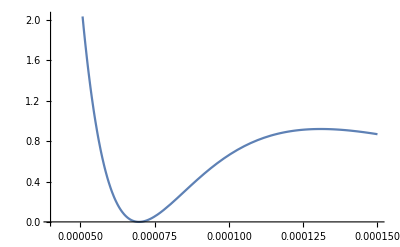

```mathematica
Ω = 2π 1 10^6;
Plot[ΦPS[0,{0,0,z},AMU, 1, Ω],{z,40μm,150μm}]
```

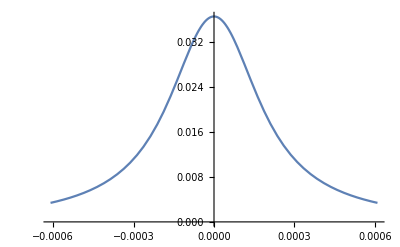

```mathematica
Plot[ϕDC[0, {x, 0, 70μm}, "DCtop3"],{x, -610μm, 610μm}]
```

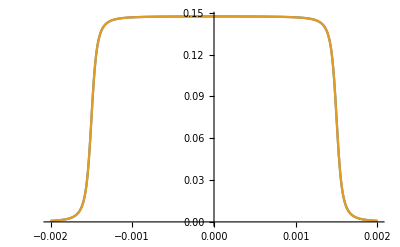

```mathematica
Plot[
{ϕDC[0, {x, 0, 70μm}, "DCintop"],
ϕDC[0, {x, 0, 70μm}, "DCinbot"],
},
{x, -2000μm, 2000μm}]
```

```mathematica
Table[ϕDC[0, {0, 0, 70μm}, label], {label, LabelsDC}]
```

{0.147408,0.147408,0.00975582,0.0220759,0.0366233,0.0220759,0.00975582,0.00975582,0.0220759,0.0366233,0.0220759,0.00975582}

#### Cover plane potential

We calculate the field of the cover plane electrode in the z=0 plane, then mirror it to the z=H plane. Of course for the potential's derivatives we have to take into account this change of coordinate : ∂/(∂z)→  -∂/(∂z) and accordingly for higher orders. That's why we us the vector a and the following matrices : Table[a⟦it⟧ a⟦jt⟧ a⟦kt⟧, {it, 1, 3}, {jt, 1, 3}, {kt, 1, 3}].

```mathematica
a={1,1,-1}; (* aid for rectifying the direction of the E-field and accordingly for the derivative tensors*)
ϕCov[0,{x_,y_,z_}]:= ComputeFinitePotential[0,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
ϕCov[1,{x_,y_,z_}]:={1,1,-1}*ComputeFinitePotential[1,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
ϕCov[2,{x_,y_,z_}]:= Table[a⟦it⟧a⟦jt⟧ ,{it,1,3},{jt,1,3}]*ComputeFinitePotential[2,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
ϕCov[3,{x_,y_,z_}]:= Table[a⟦it⟧a⟦jt⟧ a⟦kt⟧,{it,1,3},{jt,1,3},{kt,1,3}]*ComputeFinitePotential[3,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
ϕCov[4,{x_,y_,z_}]:= Table[a⟦it⟧a⟦jt⟧ a⟦kt⟧a⟦lt⟧,{it,1,3},{jt,1,3},{kt,1,3},{lt,1,3}]*ComputeFinitePotential[4,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
ϕCov[5,{x_,y_,z_}]:= Table[a⟦it⟧a⟦jt⟧ a⟦kt⟧a⟦lt⟧a⟦mt⟧,{it,1,3},{jt,1,3},{kt,1,3},{lt,1,3},{mt,1,3}]*ComputeFinitePotential[5,PixCov,{x,y,H-z},CoverPlane->{H,nH}];
HessianCov[{x_,y_,z_},VoltsCov_Real]:=ϕCov[2,{x,y,z}]*VoltsCov;
```

### Functions for evaluations

#### Secular frequencies from Hessian matrix

```mathematica
νFromCurv[Curv_]:=Sqrt[Q Curv/M]/(2π);
νFromHessianEV[Hessian_]:=Sqrt[Q Eigenvalues[Hessian]/M]/(2π);
νFromHessianDiag[Hessian_]:=Sqrt[Q Diagonal[Hessian]/M]/(2π);
```

#### ϵ - Solve for frequencies

```mathematica
ϵSolve[νList_List]:=Solve[νList⟦2⟧^2==νr^2-ϵ νList⟦1⟧^2&&νList⟦3⟧^2==νr^2-(1-ϵ) νList⟦1⟧^2&&νr>0,{νr,ϵ}]⟦1⟧;
```

```mathematica
PosLabelsDC["GND3"]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

## Export functions to Python

```mathematica
ToPython[expr_]:=Module[{expr1,expr2},
expr1=Refine[expr,{x∈Reals,y∈Reals,z>0},TimeConstraint->1];
expr2=expr1/.a_Real:>ToString@ScientificForm[a,NumberFormat->(If[#3≠"",Row[{#1,"e",#3}],ToString[#1]]&)];
StringDelete[ToString[FortranForm[expr2]],"\""]]
```

```mathematica
dir = "export";
CreateDirectory[dir]
```

D:\Scratch\pytrans-examples\models\surface_trap\data\SurfacePattern\export

PotentialsDC

```mathematica
nDC
```

12

```mathematica
PotentialsDC=Table[ToPython[ϕDC[0,{x,y,z},j]],{j,nDC}];
```

```mathematica
file=FileNameJoin[{dir, "potentialsDC.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z):\n"];
WriteString[file,"\treturn "<>PotentialsDC⟦j⟧<>"\n\n"];
,{j,nDC}]

(*Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z,H):\n"];
WriteString[file,"\treturn "<>LabelsDC⟦If[j>10,30,10]-j⟧<>"(-x,y,z,H)\n\n"];
,{j,{6,7,8,9,16,17,18,19}}]*)

WriteString[file,"All = ["<>StringRiffle[LabelsDC,","]<>"]\n\n"];

Close[file];
```

GradientsDC

```mathematica
GradientsDC=Table[Map[ToPython,ϕDC[1,{x,y,z},j]],{j,nDC}];
```

```mathematica
file=FileNameJoin[{dir, "gradientsDC.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z):\n"];
WriteString[file,"\treturn np.stack(["<>StringRiffle[GradientsDC⟦j⟧,","]<>"], axis=-1)\n\n"];
,{j,nDC}];

WriteString[file,"All = ["<>StringRiffle[LabelsDC,","]<>"]\n\n"];

Close[file];
```

HessiansDC

```mathematica
HessiansDC=Table[Map[ToPython,ϕDC[2,{x,y,z},j],{2}],{j,nDC}];
```

```mathematica
file=FileNameJoin[{dir, "hessiansDC.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z):\n"];
WriteString[file,"\txx = "<>HessiansDC⟦j,1,1⟧<>"\n"];
WriteString[file,"\txy = "<>HessiansDC⟦j,1,2⟧<>"\n"];
WriteString[file,"\txz = "<>HessiansDC⟦j,1,3⟧<>"\n"];
WriteString[file,"\tyy = "<>HessiansDC⟦j,2,2⟧<>"\n"];
WriteString[file,"\tyz = "<>HessiansDC⟦j,2,3⟧<>"\n"];
WriteString[file,"\th1 = np.asarray([[xx,xy,xz],[xy,yy,yz],[xz,yz,-xx-yy]])\n"];
WriteString[file,"\treturn h1.transpose(tuple(_ for _ in range(2, h1.ndim)) + (0, 1))\n\n"];
,{j,nDC}];

WriteString[file,"All = ["<>StringRiffle[LabelsDC,","]<>"]\n\n"];

Close[file];
```

ThirdOrderAxialDC

```mathematica
ThirdOrderAxialDC=Table[ToPython[ϕDC[3,{x,y,z},j][[1,1,1]]],{j,nDC}];
```

```mathematica
file=FileNameJoin[{dir, "third_order_axial_DC.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z):\n"];
WriteString[file,"\treturn "<>ThirdOrderAxialDC⟦j⟧<>"\n\n"];
,{j,nDC}]

(*Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z,H):\n"];
WriteString[file,"\treturn "<>LabelsDC⟦If[j>10,30,10]-j⟧<>"(-x,y,z,H)\n\n"];
,{j,{6,7,8,9,16,17,18,19}}]*)

WriteString[file,"All = ["<>StringRiffle[LabelsDC,","]<>"]\n\n"];

Close[file];
```

FourthOrderAxialDC

```mathematica
FourthOrderAxialDC=Table[ToPython[ϕDC[4,{x,y,z},j][[1,1,1,1]]],{j,nDC}];
```

```mathematica
file=FileNameJoin[{dir, "fourth_order_axial_DC.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z):\n"];
WriteString[file,"\treturn "<>FourthOrderAxialDC⟦j⟧<>"\n\n"];
,{j,nDC}]

(*Do[(* Write full expressions for electrodes. *)
WriteString[file,"def "<>LabelsDC⟦j⟧<>"(x,y,z,H):\n"];
WriteString[file,"\treturn "<>LabelsDC⟦If[j>10,30,10]-j⟧<>"(-x,y,z,H)\n\n"];
,{j,{6,7,8,9,16,17,18,19}}]*)

WriteString[file,"All = ["<>StringRiffle[LabelsDC,","]<>"]\n\n"];

Close[file];
```

Pseudopotential

```mathematica
PotentialPS=ToPython[ΦPS[0,{x,y,z},Mass,VoltRF, OmegaRF]];
```

```mathematica
GradientPS=Map[ToPython,ΦPS[1,{x,y,z},Mass,VoltRF, OmegaRF]];
```

```mathematica
HessianPS=Map[ToPython,ΦPS[2,{x,y,z},Mass,VoltRF, OmegaRF],{2}];
```

```mathematica
file=FileNameJoin[{dir, "pseudoPotential.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

WriteString[file,"def ps0(x, y, z, Mass, VoltRF, OmegaRF):\n"];
WriteString[file,"\treturn "<>PotentialPS<>"\n\n"];

WriteString[file,"def ps1(x,y,z, Mass, VoltRF, OmegaRF):\n"];
WriteString[file,"\treturn np.stack(["<>StringRiffle[GradientPS,","]<>"], axis=-1)\n\n"];

WriteString[file,"def ps2(x,y,z, Mass, VoltRF, OmegaRF):\n"];
WriteString[file,"\txx = "<>HessianPS⟦1,1⟧<>"\n"];
WriteString[file,"\txy = "<>HessianPS⟦1,2⟧<>"\n"];
WriteString[file,"\txz = "<>HessianPS⟦1,3⟧<>"\n"];
WriteString[file,"\tyy = "<>HessianPS⟦2,2⟧<>"\n"];
WriteString[file,"\tyz = "<>HessianPS⟦2,3⟧<>"\n"];
WriteString[file,"\tzz = "<>HessianPS⟦3,3⟧<>"\n"];
WriteString[file,"\th1 = np.asarray([[xx,xy,xz],[xy,yy,yz],[xz,yz,zz]])\n"];
WriteString[file,"\treturn h1.transpose(tuple(_ for _ in range(2, h1.ndim)) + (0, 1))\n\n"];

Close[file];
```

Cover

```mathematica
PotentialCov=ToPython[ϕCov[0,{x,y,z}]];
```

```mathematica
GradientCov=Map[ToPython,ϕCov[1,{x,y,z}]];
```

```mathematica
file=FileNameJoin[{dir, "cover.py"}];
Put[file];

WriteString[file,"# flake8: noqa\n"];
WriteString[file,"import numpy as np\n"];
WriteString[file,"from numpy import sqrt as Sqrt\n"];
WriteString[file,"from numpy import abs as Abs\n"];
WriteString[file,"from numpy import sign as Sign\n"];
WriteString[file,"from numpy import pi as Pi\n\n"];

WriteString[file,"def ArcTan(x,y):\n"];
WriteString[file,"\treturn np.arctan2(y,x)\n\n"];

WriteString[file,"def cov0(x,y,z):\n"];
WriteString[file,"\treturn "<>PotentialCov<>"\n\n"];

WriteString[file,"def cov1(x,y,z):\n"];
WriteString[file,"\treturn np.stack(["<>StringRiffle[GradientCov,","]<>"], axis=-1)\n\n"];

Close[file];
```